# Допълнителни задачи за числено решаване на ОДУ

## Задача 1. Разглеждаме числения метод с тегло θ y_(j+1)=y_j+hθf_(j+1)+h(1-θ)f_j

Кои методи се получават при θ = 0 и θ = 1?

За θ=0 имаме  y_(j+1)=y_j+hf_j - Явен метод на Ойлер

За θ=1 имаме  y_(j+1)=y_j+hf_(j+1)  - Неявен метод на Ойлер

Как даденият метод може да бъде изведен от явния и неявния метод на Ойлер?

За кои стойности на θ методът е неявен?

За θ≠0

Изведете условие за A-устойчивост за произволно θ .

du/dt=λu , λ<0

y_(j+1)=y_j+hθλy_(j+1)+h(1-θ)λy_j
y_(j+1)(1 - hθλ) = y_j(1 + hλ(1-θ))
y_(j+1) = (1 + hλ - hλθ)/(1 - hθλ)y_j

Abs[(1 + hλ - hλθ)/(1 - hθλ)]<1
Abs[1 +hλ/(1 - hθλ)]<1

За кои стойности на \theta методът е A-устойчив (за всяко h > 0)?

1 +hλ/(1 - hθλ)<1 <=> hλ/(1 - hθλ)<0 <=>1-hλθ > 0<=> θ > 1/λh (*)

1 +hλ/(1 - hθλ)>-1 <=> hλ/(1 - hθλ)>-2 <=> hλ>-2(1 - hθλ) <=>θ>(2+hλ)/(2hλ) (**)

От (*) и (**) и от 1/λh<(2+hλ)/(2hλ)= 1/2+1/хλ => θ>(2+hλ)/(2hλ)

За кои стойности на \theta методът е монотонен (за всяко h > 0)?

1 +hλ/(1 - hθλ)>0 <=> hλ>-1+hθλ <=> θ>(1+hλ)/hλ

Методът, който се получава при θ = 1/2 е известен като подобрен метод на Ойлер.
Приложете го за решаване на логстичното уравнение, изследвано на упражнения.
Илюстрирайте факта, че методът има втори ред на сходимост, като изследвате стойностите на абсолютната грешка при подходящи стойности на стъпката h.

## Задача 2

Да разгледаме уравнението
                               ϵ u’(t) = (1 - t)u(t) - u^2(t),   0 < t \leq 2,
при ϵ = 0.01 и начално условие u(0) = 1.

Да се реши уравнението с неявния метод на Ойлер и методите на Рунге-Кута от трети и четвърти ред, имплементирани на упражнение, при n = 30, 60, 120. Да се начертаят графиките на трите приближени решения в една координатна систма за
всяка от стойностите на n. Наблюдавате ли някакви проблеми с решението при някой от методите? На какво се дължат те?
Да се оцени реда на сходимост на трите метода, като се използва метода на Рунге за практическа оценка на реда на сходимост с три влкожени мрежи при n = 100, 200, 400 (вижзаписките).
Забележка: За проверка на коректността на получените решения, можете да използвате функцията NDSolve.

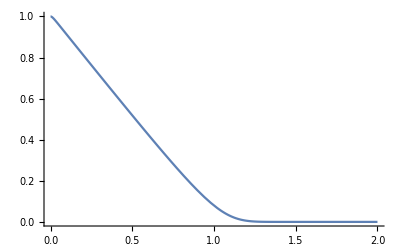

```mathematica
du[u_,t_] := 100((1-t)u-u^2)//N;
sol= NDSolve[{(1-t)u[t]-u[t]*u[t]-1/100 u'[t]==0,u[0]==1},u,{t,0,2}];
Plot[Evaluate[u[t]/.sol],{t,0,2},PlotRange->All]
```

```mathematica
FEuler[du_,u0_,t0_,T_,h_]:=Module[
{n,y,i,t},
n = (T-t0)/h;
y = Table[0, n];
y[[1]]=u0;
t=t0+h;

For[i = 1, i<n, i++,
y[[i+1]]=y[[i]]+h*du[y[[i]],t]//N;
t=t+h;
];

ret = Table[{t0+(i-1)*h,y[[i]]},{i,1,n}]
]
BEuler[du_,u0_, t0_,T_, h_]:=Module[
{n,y,i,aprox,t},
n = (T-t0)/h;
aprox = FEuler[du, u0,t0,T,h];

y = Table[0,n];
t= t0+h;
y[[1]]= u0;

For[i=1, i<n,i++,
y[[i+1]]=fy/.FindRoot[fy == y[[i]]+h*du[fy, t],{fy,aprox[[i+1,2]]}];
t=t+h;
];

ret = Table[{t0+(i-1)*h,y[[i]]},{i,1,n}]
]
```

```mathematica
ListLinePlot[FEuler[du, 1,0,2,2/30]]
```

ListLinePlot::prng: Value of option PlotRange -> {{0,1.93333},{-1.68114223098×10^3735346,1.70782}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

-Graphics-

```mathematica
Length[FEuler[du, 1,0,2,2/30]]
```

30